```mathematica
Quit
```

```mathematica
<<lilyric`
<<lilytex`
```

```mathematica
L[n_]:=(x^(n+1) D[#,x])&;
```

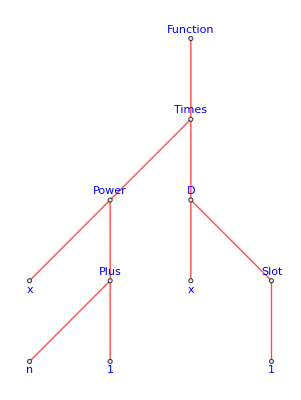

```mathematica
L[n]//TF[]//exportSVG["tree_example_Witt"]
```

$RecursionLimit::reclim2: Recursion depth of 20 exceeded during evaluation of -f.

{f,-f,{f,-f,{f,-f,{f,-f,{f,-f,{f,-f,{f,-f,{f,-f,{f,-f,{f,-f,{f,-f,{f,-f,{f,-f,{f,-f,{f,-f,{f,-f,{f,-f}}}}}}}}}}}}}}}}}

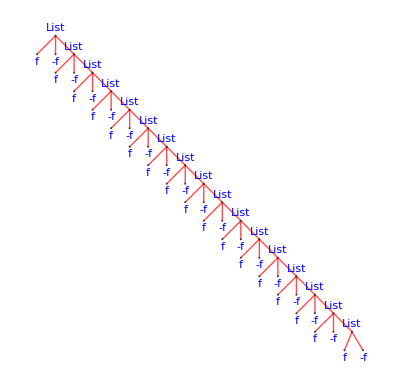

```mathematica
Block[{$RecursionLimit=20,f},
f:=-f;
Trace[f,f]
]//ReleaseHold
Out[]/.{-f->"-f"}//TF[]//exportSVG["trace1"]
```